```mathematica
ClearAll["Global`*"]
```

## Te130

```mathematica
enData1={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strData1={0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000002,0.0000000008,0.0000000035,0.0000000143,0.0000000562,0.0000002082,0.0000007305,0.0000024253,0.0000076205,0.0000226616,0.0000637826,0.0001699146,0.0004284451,0.0010226276,0.0023105905,0.0049424409,0.0100094141,0.0191940739,0.0348552678,0.0599480163,0.0976702826,0.1507733707,0.2205852354,0.3059568359,0.4024876021,0.5024275079,0.5955210592,0.6707586947,0.7186386854,0.7332857819,0.7137652649,0.6642023178,0.5927519609,0.5098610007,0.4264399337,0.3524579741,0.2961701856,0.2638522468,0.2597208920,0.2857398502,0.3412241400,0.4224394896,0.5225877525,0.6325419759,0.7424128795,0.8435958318,0.9305805641,1.0017350113,1.0586083242,1.1039318078,1.1391364803,1.1625137108,1.1689278535,1.1513201302,1.1034349710,1.0226454790,0.9117166979,0.7788239132,0.6358863804,0.4959246738,0.3704241200,0.2675196987,0.1913562784,0.1424777898,0.1187824294,0.1165402669,0.1311533349,0.1576079920,0.1907799280,0.2258144947,0.2587118036,0.2870617414,0.3106997719,0.3319814507,0.3554434344,0.3868060044,0.4314991452,0.4930698044,0.5718883504,0.6645032940,0.7638265552,0.8601235857,0.9425931820,1.0011984073,1.0283783911,1.0203285981,0.9776547330,0.9053385255,0.8120652482,0.7090400830,0.6084727645,0.5219499212,0.4589387904,0.4256536896,0.4244482550,0.4537772377,0.5086401289,0.5813317179,0.6623246734,0.7411947549,0.8076150757,0.8525070811,0.8693788511,0.8557131060,0.8140779129,0.7525522730,0.6841787000,0.6254700740,0.5944023802,0.6086614942,0.6850315724,0.8406036672,1.0958865913,1.4789516680,2.0286495571,2.7941480168,3.8281554034,5.1726851050,6.8390288265,8.7869261015,10.9103167181,13.0370918125,14.9472180236,16.4080820409,17.2197173410,17.2581365270,16.5042759121,15.0497006786,13.0771289179,10.8215353953,8.5232166348,6.3856989146,4.5484451942,3.0784798084,1.9788381217,1.2074844687,0.6991387453,0.3839602234,0.1999392618,0.0986878798,0.0461598548,0.0204548297,0.0085855416,0.0034127287,0.0012844903,0.0004577172,0.0001544016,0.0000493007,0.0000148992,0.0000042614,0.0000011535,0.0000002954,0.0000000716,0.0000000164,0.0000000036,0.0000000007,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
enData2={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strData2={0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000001,0.0000000002,0.0000000005,0.0000000013,0.0000000035,0.0000000088,0.0000000209,0.0000000472,0.0000001017,0.0000002084,0.0000004069,0.0000007576,0.0000013450,0.0000022779,0.0000036817,0.0000056809,0.0000083711,0.0000117845,0.0000158555,0.0000203986,0.0000251097,0.0000295990,0.0000334559,0.0000363367,0.0000380601,0.0000386959,0.0000386338,0.0000386302,0.0000398232,0.0000437025,0.0000520003,0.0000664628,0.0000884784,0.0001185974,0.0001560552,0.0001984923,0.0002420719,0.0002821145,0.0003141886,0.0003353826,0.0003453334,0.0003465930,0.0003440915,0.0003437643,0.0003507218,0.0003675369,0.0003932253,0.0004232843,0.0004508138,0.0004683809,0.0004700375,0.0004528597,0.0004175625,0.0003680787,0.0003103474,0.0002507816,0.0001949099,0.0001465331,0.0001074924,0.0000779350,0.0000568517,0.0000426582,0.0000336667,0.0000283847,0.0000256529,0.0000246736,0.0000249867,0.0000264345,0.0000291249,0.0000333800,0.0000396377,0.0000482911,0.0000594791,0.0000728852,0.0000876314,0.0001023420,0.0001154038,0.0001253749,0.0001314318,0.0001337305,0.0001336037,0.0001336034,0.0001374738,0.0001501665,0.0001779581,0.0002286266,0.0003115129,0.0004371938,0.0006164581,0.0008583439,0.0011672179,0.0015392667,0.0019592638,0.0023988892,0.0028179293,0.0031691345,0.0034063659,0.0034942800,0.0034167981,0.0031815750,0.0028188028,0.0023745720,0.0019008672,0.0014452792,0.0010432907,0.0007147572,0.0004645990,0.0002864497,0.0001674813,0.0000928411,0.0000487853,0.0000242962,0.0000114662,0.0000051271,0.0000021719,0.0000008715,0.0000003312,0.0000001192,0.0000000406,0.0000000131,0.0000000040,0.0000000012,0.0000000003,0.0000000001,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
```

## Xe130

```mathematica
enData3={-0.9000000000,-0.8000000000,-0.7000000000,-0.6000000000,-0.5000000000,-0.4000000000,-0.3000000000,-0.2000000000,-0.1000000000,0.0000000000,0.1000000000,0.2000000000,0.3000000000,0.4000000000,0.5000000000,0.6000000000,0.7000000000,0.8000000000,0.9000000000,1.0000000000,1.1000000000,1.2000000000,1.3000000000,1.4000000000,1.5000000000,1.6000000000,1.7000000000,1.8000000000,1.9000000000,2.0000000000,2.1000000000,2.2000000000,2.3000000000,2.4000000000,2.5000000000,2.6000000000,2.7000000000,2.8000000000,2.9000000000,3.0000000000,3.1000000000,3.2000000000,3.3000000000,3.4000000000,3.5000000000,3.6000000000,3.7000000000,3.8000000000,3.9000000000,4.0000000000,4.1000000000,4.2000000000,4.3000000000,4.4000000000,4.5000000000,4.6000000000,4.7000000000,4.8000000000,4.9000000000,5.0000000000,5.1000000000,5.2000000000,5.3000000000,5.4000000000,5.5000000000,5.6000000000,5.7000000000,5.8000000000,5.9000000000,6.0000000000,6.1000000000,6.2000000000,6.3000000000,6.4000000000,6.5000000000,6.6000000000,6.7000000000,6.8000000000,6.9000000000,7.0000000000,7.1000000000,7.2000000000,7.3000000000,7.4000000000,7.5000000000,7.6000000000,7.7000000000,7.8000000000,7.9000000000,8.0000000000,8.1000000000,8.2000000000,8.3000000000,8.4000000000,8.5000000000,8.6000000000,8.7000000000,8.8000000000,8.9000000000,9.0000000000,9.1000000000,9.2000000000,9.3000000000,9.4000000000,9.5000000000,9.6000000000,9.7000000000,9.8000000000,9.9000000000,10.0000000000,10.1000000000,10.2000000000,10.3000000000,10.4000000000,10.5000000000,10.6000000000,10.7000000000,10.8000000000,10.9000000000,11.0000000000,11.1000000000,11.2000000000,11.3000000000,11.4000000000,11.5000000000,11.6000000000,11.7000000000,11.8000000000,11.9000000000,12.0000000000,12.1000000000,12.2000000000,12.3000000000,12.4000000000,12.5000000000,12.6000000000,12.7000000000,12.8000000000,12.9000000000,13.0000000000,13.1000000000,13.2000000000,13.3000000000,13.4000000000,13.5000000000,13.6000000000,13.7000000000,13.8000000000,13.9000000000,14.0000000000,14.1000000000,14.2000000000,14.3000000000,14.4000000000,14.5000000000,14.6000000000,14.7000000000,14.8000000000,14.9000000000,15.0000000000,15.1000000000,15.2000000000,15.3000000000,15.4000000000,15.5000000000,15.6000000000,15.7000000000,15.8000000000,15.9000000000,16.0000000000,16.1000000000,16.2000000000,16.3000000000,16.4000000000,16.5000000000,16.6000000000,16.7000000000,16.8000000000,16.9000000000,17.0000000000,17.1000000000,17.2000000000,17.3000000000,17.4000000000,17.5000000000,17.6000000000,17.7000000000,17.8000000000,17.9000000000,18.0000000000,18.1000000000,18.2000000000,18.3000000000,18.4000000000,18.5000000000,18.6000000000,18.7000000000,18.8000000000,18.9000000000,19.0000000000,19.1000000000,19.2000000000,19.3000000000,19.4000000000,19.5000000000,19.6000000000,19.7000000000,19.8000000000,19.9000000000,20.0000000000,20.1000000000,20.2000000000,20.3000000000,20.4000000000,20.5000000000,20.6000000000,20.7000000000,20.8000000000,20.9000000000,21.0000000000};
strData3={0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000001,0.0000000003,0.0000000008,0.0000000026,0.0000000078,0.0000000219,0.0000000585,0.0000001484,0.0000003570,0.0000008160,0.0000017734,0.0000036683,0.0000072311,0.0000136039,0.0000244642,0.0000421272,0.0000695917,0.0001104931,0.0001689364,0.0002492026,0.0003553728,0.0004909938,0.0006590252,0.0008624246,0.0011057831,0.0013982944,0.0017579355,0.0022159936,0.0028201190,0.0036332562,0.0047256978,0.0061587198,0.0079610927,0.0101036833,0.0124808257,0.0149080199,0.0171421921,0.0189234472,0.0200285466,0.0203203289,0.0197773643,0.0184948535,0.0166582780,0.0145006566,0.0122582996,0.0101374562,0.0082973309,0.0068475175,0.0058533734,0.0053426229,0.0053096075,0.0057178073,0.0065040830,0.0075879971,0.0088865390,0.0103301701,0.0118729021,0.0134895300,0.0151579556,0.0168321061,0.0184175770,0.0197638720,0.0206820403,0.0209861342,0.0205457953,0.0193308564,0.0174305790,0.0150395353,0.0124149377,0.0098205541,0.0074758260,0.0055245614,0.0040284109,0.0029808547,0.0023315973,0.0020106692,0.0019451706,0.0020669581,0.0023140390,0.0026304257,0.0029684333,0.0032947643,0.0035986423,0.0038981274,0.0042404339,0.0046936713,0.0053302938,0.0062055963,0.0073367585,0.0086884607,0.0101697622,0.0116441003,0.0129507620,0.0139330896,0.0144669922,0.0144835361,0.0139812502,0.0130264828,0.0117427187,0.0102915877,0.0088492393,0.0075820447,0.0066253729,0.0060684779,0.0059472371,0.0062447252,0.0068978917,0.0078076405,0.0088499095,0.0098868197,0.0107787543,0.0113990830,0.0116522667,0.0114934365,0.0109446349,0.0101016716,0.0091272783,0.0082307527,0.0076398956,0.0075754749,0.0082397424,0.0098275499,0.0125610918,0.0167380259,0.0227702827,0.0311822177,0.0425384072,0.0572883194,0.0755465450,0.0968640768,0.1200724310,0.1432822538,0.1640839514,0.1799366437,0.1886638052,0.1889258786,0.1805333223,0.1645044302,0.1428483570,0.1181377399,0.0929958982,0.0696389747,0.0495807459,0.0335439391,0.0215543987,0.0131484280,0.0076109597,0.0041788956,0.0021756370,0.0010736864,0.0005021276,0.0002224799,0.0000933719,0.0000371117,0.0000139671,0.0000049767,0.0000016787,0.0000005360,0.0000001620,0.0000000463,0.0000000125,0.0000000032,0.0000000008,0.0000000002,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000,0.0000000000};
```

## Numerical params

```mathematica
elem[el_,n_]:=Style[Row[{Superscript["",n],StringTemplate["``"][el]}]];
xdp=0.325;
chi12=0.3;
el1=elem["Te",130];
el2=elem["Xe",130];
```

## Figures

### Figure1

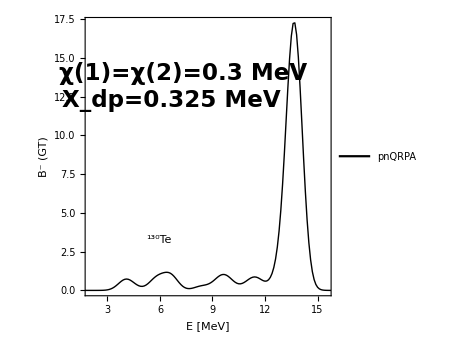

```mathematica
tableFig1=Table[{enData1[[i]],strData1[[i]]},{i,1,Length[strData1]}];
fig1=ListPlot[tableFig1,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{2,15.5},Full},FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.8}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[el1,23,Bold,Black,FontFamily->"Times"]],Scaled[{0.3,0.2}]]}];
Show[fig1]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_7/new_figs/fig1_set7.pdf",Show[fig1],ImageResolution->1200];
```

### Figure2

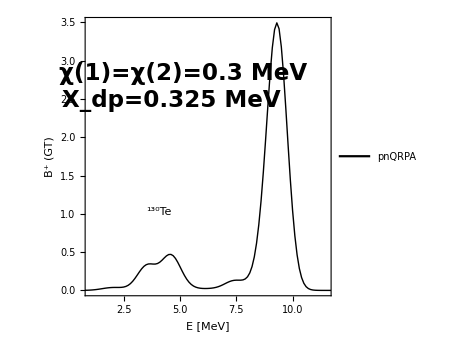

```mathematica
tableFig2=Table[{enData2[[i]],strData2[[i]]*1000},{i,1,Length[strData2]}];
fig2=ListPlot[tableFig2,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{1,11.5},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.8}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[el1,23,Bold,Black,FontFamily->"Times"]],Scaled[{0.3,0.3}]]}];
Show[fig2]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_7/new_figs/fig2_set7.pdf",Show[fig2],ImageResolution->1200];
```

### Figure3

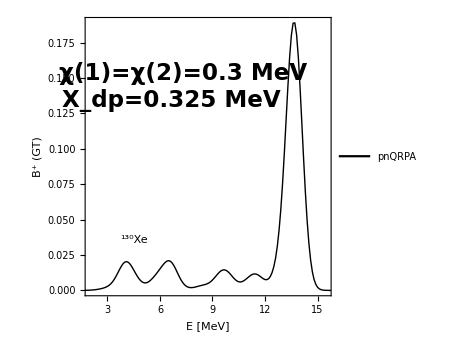

```mathematica
tableFig3=Table[{enData3[[i]],strData3[[i]]},{i,1,Length[strData3]}];
fig3=ListPlot[tableFig3,Joined->True,ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{2,15.5},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style[StringTemplate["χ(1)=χ(2)=`` MeV"][chi12],23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.8}]],Inset[Style[StringTemplate["X_dp=`` MeV"][xdp],23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.7}]],Inset[Framed[Style[el2,23,Bold,Black,FontFamily->"Times"]],Scaled[{0.2,0.2}]]}];
Show[fig3]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_7/new_figs/fig3_set7.pdf",Show[fig3],ImageResolution->1200];
```